h yn λ

h λ (yn+(h yn λ)/2)

h λ (yn+1/4 h yn λ (2+h λ))

h λ (yn+h λ (yn+1/4 h yn λ (2+h λ)))

1+z+z^2/2+z^3/6+z^4/24

{{0,0},{0,-2 √2},{0,2 √2},{1/3 (-4-10 (2/(-43+9 √29))^(1/3)+2^(2/3) (-43+9 √29)^(1/3)),0}}

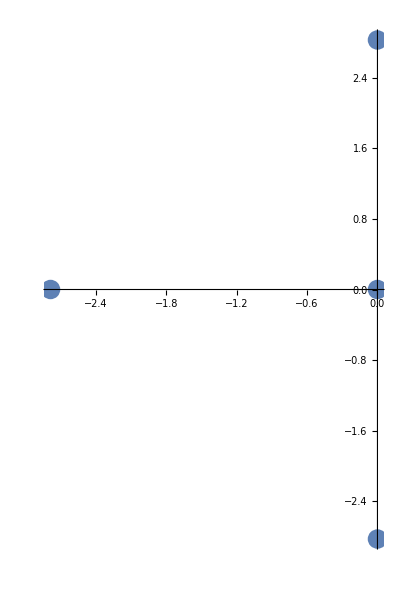

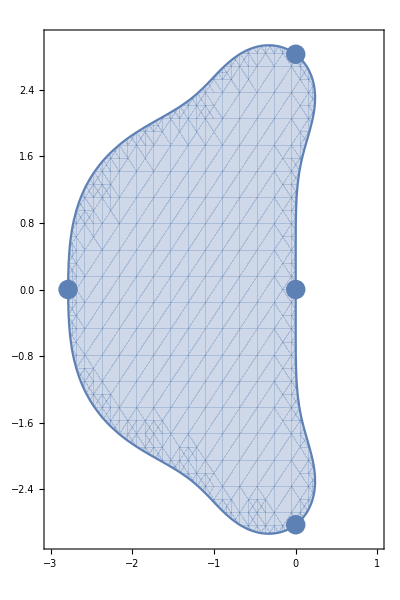

```mathematica
k1=h λ yn
k2 = h λ(yn + 1/2 k1)//FullSimplify
k3=h λ(yn + 1/2 k2)//FullSimplify
k4 = h λ(yn + k3)//FullSimplify
f[z_]=((yn+1/6(k1+2k2+2k3+k4))/yn)/.h->z/λ//Expand
vals=ReIm[Assuming[Re[z]==0∨Im[z]==0,SolveValues[Abs[f[z]]==1,z]]]//ToRadicals
points=ListPlot[vals,PlotStyle->PointSize[0.035],AspectRatio->6/4]
trueReg=ComplexRegionPlot[Abs[f[z]]<1,{z,-3(1+ⅈ),3(1/3+ⅈ)}];
Show[trueReg,points,AspectRatio->6/4]
```

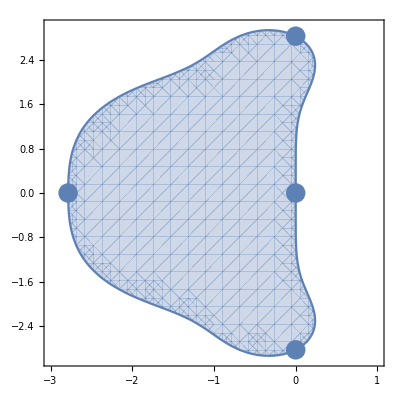

```mathematica
Manipulate[ContourPlot[ComplexExpand[Abs[f[x+ⅈ y]]^2]==ϵ,{x,-3,0.5},{y,-3,3},PlotPoints->50],{ϵ,0.001,1}]
```

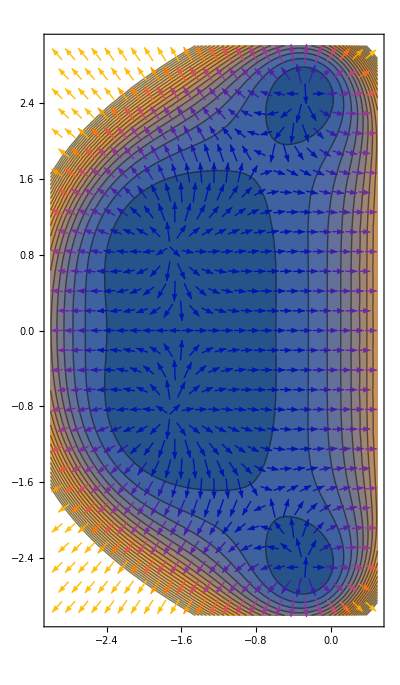

```mathematica
Show[ContourPlot[ComplexExpand[Abs[f[x+ⅈ y]]^2],{x,-3,0.5},{y,-3,3},AspectRatio->6/3.5,Contours->20],VectorPlot[Evaluate[∇_{x,y} ComplexExpand[Abs[f[x+ⅈ y]]^2]],{x,-3,0.5},{y,-3,3},VectorPoints->Fine]]
```

{2+4 x[θ]+4 x[θ]^2+(8 x[θ]^3)/3+(5 x[θ]^4)/4+(5 x[θ]^5)/12+(7 x[θ]^6)/72+x[θ]^7/72+1/2 x[θ]^2 y[θ]^2+1/2 x[θ]^3 y[θ]^2+5/24 x[θ]^4 y[θ]^2+1/24 x[θ]^5 y[θ]^2-y[θ]^4/12+1/12 x[θ] y[θ]^4+1/8 x[θ]^2 y[θ]^4+1/24 x[θ]^3 y[θ]^4+y[θ]^6/72+1/72 x[θ] y[θ]^6,1/3 x[θ]^3 y[θ]+1/4 x[θ]^4 y[θ]+1/12 x[θ]^5 y[θ]+1/72 x[θ]^6 y[θ]-1/3 x[θ] y[θ]^3+1/6 x[θ]^2 y[θ]^3+1/6 x[θ]^3 y[θ]^3+1/24 x[θ]^4 y[θ]^3-y[θ]^5/12+1/12 x[θ] y[θ]^5+1/24 x[θ]^2 y[θ]^5+y[θ]^7/72}

{InterpolatingFunction[…][θ],InterpolatingFunction[…][θ]}

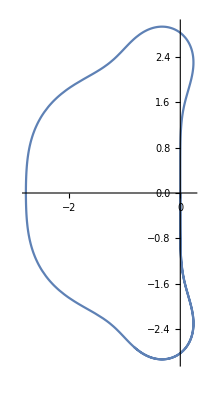

```mathematica
grad=Evaluate[∇_{x,y} ComplexExpand[Abs[f[x+ⅈ y]]^2]]/.{x->x[θ],y->y[θ]}
sol[θ_]=NDSolveValue[{x'[θ]==grad[[2]],y'[θ]==-grad[[1]],y[0]==0,x[0]==0},{x[θ],y[θ]},{θ,0,2π}]
ParametricPlot[sol[θ],{θ,0,2π}]
```

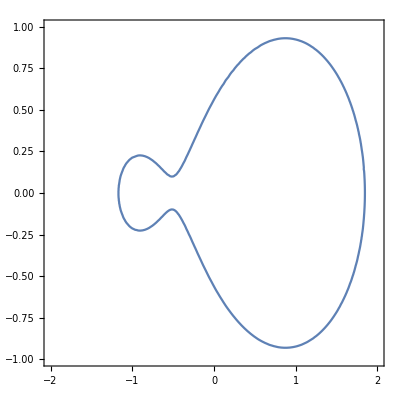

{0,0}

```mathematica
p[z_]=(z+1)(z-1)^3;
f[x_,y_]=ComplexExpand[Abs[p[x+ⅈ y]]^2];
norm=Norm[∇_{x,y} f[x,y]];
ContourPlot[f[x,y]==3,{x,-2,2},{y,-1,1}]
Evaluate[∇_{x,y} f[x,y]]/.{x->1,y->0}
```

```mathematica
DSolveValue[{
y'[t]==C[1] x[t]+C[2] y[t],
x'[t]==C[3] x[t]+C[4] y[t],
x[0]==a,y[0]==b},
{x[t],y[t]},t]//FullSimplify
```

{ⅇ^(1/2 t (C[2]+C[3])) (a Cosh[1/2 t √((C[2]-C[3])^2+4 C[1] C[4])]+((a (-C[2]+C[3])+2 b C[4]) Sinh[1/2 t √((C[2]-C[3])^2+4 C[1] C[4])])/(√((C[2]-C[3])^2+4 C[1] C[4]))),ⅇ^(1/2 t (C[2]+C[3])) (b Cosh[1/2 t √((C[2]-C[3])^2+4 C[1] C[4])]+((2 a C[1]+b (C[2]-C[3])) Sinh[1/2 t √((C[2]-C[3])^2+4 C[1] C[4])])/(√((C[2]-C[3])^2+4 C[1] C[4])))}